# Three Experiences From ODE simulation Sahin Model

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<Booned`
```

```mathematica
<<Bi4Back`
```

```mathematica
<<Functionsneededpackage`
```

```mathematica
Unprotect[t];Clear[t];Protect[t];
```

## RESEAU BOOLEEN EXEMPLE

```mathematica
FB= {ERBB1->EGF,ERBB2->EGF,ERBB3->EGF,ERBB12->ERBB1&&ERBB2,ERBB13->ERBB1&&ERBB3,ERBB23->ERBB2&&ERBB3,IGF1R->(AKT1&&!ERBB23)||(ERa&&!ERBB23),ERa->AKT1||MEK1,cMYC->AKT1||ERa||MEK1,AKT1->ERBB1||ERBB12||ERBB13||ERBB23||IGF1R,MEK1->ERBB1||ERBB12||ERBB13||ERBB23||IGF1R,CDK2->CyclinE1&&!p21&&!p27,CDK4->CyclinD1&&!p21&&!p27,CDK6->CyclinD1,CyclinD1->AKT1||cMYC||ERa||MEK1,CyclinE1->cMYC,p21->!AKT1&&!CDK4&&!cMYC&&ERa,p27->!AKT1&&!CDK2&&!CDK4&&!cMYC&&ERa,pRB->CDK4&&CDK6,EGF->EGF};
```

```mathematica
StableFB=Association/@StableStates[FB]
```

{<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→True,ERa→True,ERBB1→True,ERBB12→True,ERBB13→True,ERBB2→True,ERBB23→True,ERBB3→True,IGF1R→False,MEK1→True,p21→False,p27→False,pRB→True|>,<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→False,ERa→True,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→True,MEK1→True,p21→False,p27→False,pRB→True|>,<|AKT1→False,CDK2→False,CDK4→False,CDK6→False,cMYC→False,CyclinD1→False,CyclinE1→False,EGF→False,ERa→False,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→False,MEK1→False,p21→False,p27→False,pRB→False|>}

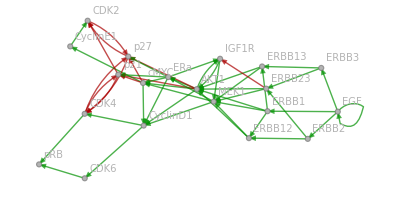

```mathematica
IG=NiceIG[InteractionGraphSimple[FB]]
```

## SIMULATION

```mathematica
name="Sahin Model"
```

Sahin Model

### Parameters

Expression rate

```mathematica
κ= AssociationThread[Keys[FB],2]
```

<|ERBB1→2,ERBB2→2,ERBB3→2,ERBB12→2,ERBB13→2,ERBB23→2,IGF1R→2,ERa→2,cMYC→2,AKT1→2,MEK1→2,CDK2→2,CDK4→2,CDK6→2,CyclinD1→2,CyclinE1→2,p21→2,p27→2,pRB→2,EGF→2|>

Degradation rate

```mathematica
γ=AssociationThread[Keys[FB],0.5]
```

<|ERBB1→0.5,ERBB2→0.5,ERBB3→0.5,ERBB12→0.5,ERBB13→0.5,ERBB23→0.5,IGF1R→0.5,ERa→0.5,cMYC→0.5,AKT1→0.5,MEK1→0.5,CDK2→0.5,CDK4→0.5,CDK6→0.5,CyclinD1→0.5,CyclinE1→0.5,p21→0.5,p27→0.5,pRB→0.5,EGF→0.5|>

Threshold for being activated or inhibited.

```mathematica
θ=<|ERBB1->0.6480041908485151,ERBB2->0.5098015695513473,ERBB3->0.5970797623452866,ERBB12->0.600305137191748,ERBB13->0.6495039840039982,ERBB23->0.3513219029300372,IGF1R->0.503817870709836,ERa->0.45897426813416714,cMYC->0.5074664081405877,AKT1->0.42489773221659816,MEK1->0.39176290371400035,CDK2->0.39185130307766297,CDK4->0.37029027505747064,CDK6->0.45738484367930565,CyclinD1->0.5689307426278277,CyclinE1->0.39061583915870773,p21->0.6317948240918596,p27->0.403052759585376,pRB->0.47467952840746636,EGF->0.35952065550493956|> (*Threshold are generated randomly using the function Thresholding, see the fuction  in the package Functionsneeded*)
```

<|ERBB1→0.648004,ERBB2→0.509802,ERBB3→0.59708,ERBB12→0.600305,ERBB13→0.649504,ERBB23→0.351322,IGF1R→0.503818,ERa→0.458974,cMYC→0.507466,AKT1→0.424898,MEK1→0.391763,CDK2→0.391851,CDK4→0.37029,CDK6→0.457385,CyclinD1→0.568931,CyclinE1→0.390616,p21→0.631795,p27→0.403053,pRB→0.47468,EGF→0.359521|>

```mathematica
Highlighted[TableForm[{Mean[θ],StandardDeviation[θ]}]]
```

0.484553
0.101171

### For a stable state

```mathematica
stablestate=StableFB[[1]]
```

<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→True,ERa→True,ERBB1→True,ERBB12→True,ERBB13→True,ERBB2→True,ERBB23→True,ERBB3→True,IGF1R→False,MEK1→True,p21→False,p27→False,pRB→True|>

```mathematica
initialcondition=<|AKT1->1,CDK2->1,CDK4->1,CDK6->1,cMYC->1,CyclinD1->1,CyclinE1->1,EGF->1,ERa->1,ERBB1->1,ERBB12->1,ERBB13->1,ERBB2->1,ERBB23->1,ERBB3->1,IGF1R->0.3,MEK1->1,p21->0.2,p27->0.2,pRB->1|>
```

<|AKT1→1,CDK2→1,CDK4→1,CDK6→1,cMYC→1,CyclinD1→1,CyclinE1→1,EGF→1,ERa→1,ERBB1→1,ERBB12→1,ERBB13→1,ERBB2→1,ERBB23→1,ERBB3→1,IGF1R→0.3,MEK1→1,p21→0.2,p27→0.2,pRB→1|>

#### ODE

```mathematica
Framed@TableForm[
system=BooleanToODE[FB,t,κ,γ,θ, initialcondition,{hillm,hillp}]]
```

ERBB1'[t]==-0.5 ERBB1[t]+2 hillp[EGF[t],0.359521]
ERBB1[0]==1
ERBB2'[t]==-0.5 ERBB2[t]+2 hillp[EGF[t],0.359521]
ERBB2[0]==1
ERBB3'[t]==-0.5 ERBB3[t]+2 hillp[EGF[t],0.359521]
ERBB3[0]==1
ERBB12'[t]==-0.5 ERBB12[t]+2 hillp[ERBB1[t],0.648004] hillp[ERBB2[t],0.509802]
ERBB12[0]==1
ERBB13'[t]==-0.5 ERBB13[t]+2 hillp[ERBB1[t],0.648004] hillp[ERBB3[t],0.59708]
ERBB13[0]==1
ERBB23'[t]==-0.5 ERBB23[t]+2 hillp[ERBB2[t],0.509802] hillp[ERBB3[t],0.59708]
ERBB23[0]==1
IGF1R'[t]==2 (hillm[ERBB23[t],0.351322] hillp[AKT1[t],0.424898]+hillm[ERBB23[t],0.351322] hillp[ERa[t],0.458974])-0.5 IGF1R[t]
IGF1R[0]==0.3
ERa'[t]==-0.5 ERa[t]+2 (hillp[AKT1[t],0.424898]+hillp[MEK1[t],0.391763])
ERa[0]==1
cMYC'[t]==-0.5 cMYC[t]+2 (hillp[AKT1[t],0.424898]+hillp[ERa[t],0.458974]+hillp[MEK1[t],0.391763])
cMYC[0]==1
AKT1'[t]==-0.5 AKT1[t]+2 (hillp[ERBB1[t],0.648004]+hillp[ERBB12[t],0.600305]+hillp[ERBB13[t],0.649504]+hillp[ERBB23[t],0.351322]+hillp[IGF1R[t],0.503818])
AKT1[0]==1
MEK1'[t]==2 (hillp[ERBB1[t],0.648004]+hillp[ERBB12[t],0.600305]+hillp[ERBB13[t],0.649504]+hillp[ERBB23[t],0.351322]+hillp[IGF1R[t],0.503818])-0.5 MEK1[t]
MEK1[0]==1
CDK2'[t]==-0.5 CDK2[t]+2 hillm[p21[t],0.631795] hillm[p27[t],0.403053] hillp[CyclinE1[t],0.390616]
CDK2[0]==1
CDK4'[t]==-0.5 CDK4[t]+2 hillm[p21[t],0.631795] hillm[p27[t],0.403053] hillp[CyclinD1[t],0.568931]
CDK4[0]==1
CDK6'[t]==-0.5 CDK6[t]+2 hillp[CyclinD1[t],0.568931]
CDK6[0]==1
CyclinD1'[t]==-0.5 CyclinD1[t]+2 (hillp[AKT1[t],0.424898]+hillp[cMYC[t],0.507466]+hillp[ERa[t],0.458974]+hillp[MEK1[t],0.391763])
CyclinD1[0]==1
CyclinE1'[t]==-0.5 CyclinE1[t]+2 hillp[cMYC[t],0.507466]
CyclinE1[0]==1
p21'[t]==2 hillm[AKT1[t],0.424898] hillm[CDK4[t],0.37029] hillm[cMYC[t],0.507466] hillp[ERa[t],0.458974]-0.5 p21[t]
p21[0]==0.2
p27'[t]==2 hillm[AKT1[t],0.424898] hillm[CDK2[t],0.391851] hillm[CDK4[t],0.37029] hillm[cMYC[t],0.507466] hillp[ERa[t],0.458974]-0.5 p27[t]
p27[0]==0.2
pRB'[t]==2 hillp[CDK4[t],0.37029] hillp[CDK6[t],0.457385]-0.5 pRB[t]
pRB[0]==1
EGF'[t]==-0.5 EGF[t]+2 hillp[EGF[t],0.359521]
EGF[0]==1

#### Experiments

```mathematica
exp=ThreeExperienceFromODE[FB,system,25,stablestate,θ]
```

<|0.02→<|ERBB1→1.03,ERBB2→1.03,ERBB3→1.03,ERBB12→1.03,ERBB13→1.03,ERBB23→1.03,IGF1R→0.297,ERa→1.07,cMYC→1.11,AKT1→1.15,MEK1→1.15,CDK2→1.03,CDK4→1.03,CDK6→1.03,CyclinD1→1.15,CyclinE1→1.03,p21→0.198,p27→0.198,pRB→1.03,EGF→1.03|>,12.49→<|ERBB1→3.99,ERBB2→3.99,ERBB3→3.99,ERBB12→3.99,ERBB13→3.99,ERBB23→3.99,IGF1R→0.000582,ERa→7.99,cMYC→12.,AKT1→16.,MEK1→16.,CDK2→3.99,CDK4→3.99,CDK6→3.99,CyclinD1→16.,CyclinE1→3.99,p21→0.000388,p27→0.000388,pRB→3.99,EGF→3.99|>,25.→<|ERBB1→4.,ERBB2→4.,ERBB3→4.,ERBB12→4.,ERBB13→4.,ERBB23→4.,IGF1R→0,ERa→8.,cMYC→12.,AKT1→16.,MEK1→16.,CDK2→4.,CDK4→4.,CDK6→4.,CyclinD1→16.,CyclinE1→4.,p21→0,p27→0,pRB→4.,EGF→4.|>|>

```mathematica
Epil=Keys[exp];
```

```mathematica
fun=#[t]&/@Keys[FB];
```

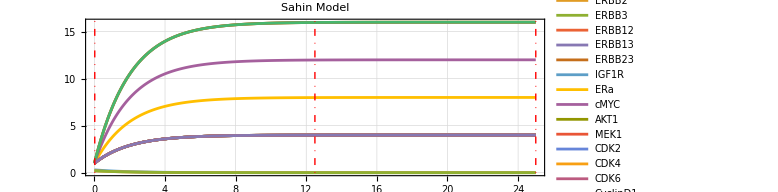

```mathematica
Plot[Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,25}]],{t,0,25}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel-> name, ImageSize->Large,Epilog-> {Thick,DotDashed, Red, Line[{{Epil[[1]],0},{Epil[[1]],20}}] ,Line[{{Epil[[2]],0},{Epil[[2]],20}}], Line[{{Epil[[3]],0},{Epil[[3]],20}}]}]
```

```mathematica
result=ThreeExperimentsBinarisation[IG,Values[exp] , stablestate]
```

{<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→True,ERa→True,ERBB1→True,ERBB12→True,ERBB13→True,ERBB2→True,ERBB23→True,ERBB3→True,IGF1R→False,MEK1→True,p21→False,p27→False,pRB→True|>,<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→True,ERa→True,ERBB1→True,ERBB12→True,ERBB13→True,ERBB2→True,ERBB23→True,ERBB3→True,IGF1R→False,MEK1→True,p21→False,p27→False,pRB→True|>,<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→True,ERa→True,ERBB1→True,ERBB12→True,ERBB13→True,ERBB2→True,ERBB23→True,ERBB3→True,IGF1R→False,MEK1→True,p21→False,p27→False,pRB→True|>}

```mathematica
dis=Distanceofdissimilarity[result,stablestate]
```

{0,0,0}

### For stable state

```mathematica
stablestate=StableFB[[2]]
```

<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→False,ERa→True,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→True,MEK1→True,p21→False,p27→False,pRB→True|>

```mathematica
initialcondition=<|AKT1->1,CDK2->1,CDK4->1,CDK6->1,cMYC->1,CyclinD1->1,CyclinE1->1,EGF->0.2,ERa->1,ERBB1->0.3,ERBB12->0.4,ERBB13->0.1,ERBB2->0.2,ERBB23->0.3,ERBB3->0.2,IGF1R->1,MEK1->1,p21->0.3,p27->0.3,pRB->1|>
```

<|AKT1→1,CDK2→1,CDK4→1,CDK6→1,cMYC→1,CyclinD1→1,CyclinE1→1,EGF→0.2,ERa→1,ERBB1→0.3,ERBB12→0.4,ERBB13→0.1,ERBB2→0.2,ERBB23→0.3,ERBB3→0.2,IGF1R→1,MEK1→1,p21→0.3,p27→0.3,pRB→1|>

#### ODE

```mathematica
Framed@TableForm[
system=BooleanToODE[FB,t,κ,γ,θ, initialcondition,{hillm,hillp}]]
```

ERBB1'[t]==-0.5 ERBB1[t]+2 hillp[EGF[t],0.359521]
ERBB1[0]==0.3
ERBB2'[t]==-0.5 ERBB2[t]+2 hillp[EGF[t],0.359521]
ERBB2[0]==0.2
ERBB3'[t]==-0.5 ERBB3[t]+2 hillp[EGF[t],0.359521]
ERBB3[0]==0.2
ERBB12'[t]==-0.5 ERBB12[t]+2 hillp[ERBB1[t],0.648004] hillp[ERBB2[t],0.509802]
ERBB12[0]==0.4
ERBB13'[t]==-0.5 ERBB13[t]+2 hillp[ERBB1[t],0.648004] hillp[ERBB3[t],0.59708]
ERBB13[0]==0.1
ERBB23'[t]==-0.5 ERBB23[t]+2 hillp[ERBB2[t],0.509802] hillp[ERBB3[t],0.59708]
ERBB23[0]==0.3
IGF1R'[t]==2 (hillm[ERBB23[t],0.351322] hillp[AKT1[t],0.424898]+hillm[ERBB23[t],0.351322] hillp[ERa[t],0.458974])-0.5 IGF1R[t]
IGF1R[0]==1
ERa'[t]==-0.5 ERa[t]+2 (hillp[AKT1[t],0.424898]+hillp[MEK1[t],0.391763])
ERa[0]==1
cMYC'[t]==-0.5 cMYC[t]+2 (hillp[AKT1[t],0.424898]+hillp[ERa[t],0.458974]+hillp[MEK1[t],0.391763])
cMYC[0]==1
AKT1'[t]==-0.5 AKT1[t]+2 (hillp[ERBB1[t],0.648004]+hillp[ERBB12[t],0.600305]+hillp[ERBB13[t],0.649504]+hillp[ERBB23[t],0.351322]+hillp[IGF1R[t],0.503818])
AKT1[0]==1
MEK1'[t]==2 (hillp[ERBB1[t],0.648004]+hillp[ERBB12[t],0.600305]+hillp[ERBB13[t],0.649504]+hillp[ERBB23[t],0.351322]+hillp[IGF1R[t],0.503818])-0.5 MEK1[t]
MEK1[0]==1
CDK2'[t]==-0.5 CDK2[t]+2 hillm[p21[t],0.631795] hillm[p27[t],0.403053] hillp[CyclinE1[t],0.390616]
CDK2[0]==1
CDK4'[t]==-0.5 CDK4[t]+2 hillm[p21[t],0.631795] hillm[p27[t],0.403053] hillp[CyclinD1[t],0.568931]
CDK4[0]==1
CDK6'[t]==-0.5 CDK6[t]+2 hillp[CyclinD1[t],0.568931]
CDK6[0]==1
CyclinD1'[t]==-0.5 CyclinD1[t]+2 (hillp[AKT1[t],0.424898]+hillp[cMYC[t],0.507466]+hillp[ERa[t],0.458974]+hillp[MEK1[t],0.391763])
CyclinD1[0]==1
CyclinE1'[t]==-0.5 CyclinE1[t]+2 hillp[cMYC[t],0.507466]
CyclinE1[0]==1
p21'[t]==2 hillm[AKT1[t],0.424898] hillm[CDK4[t],0.37029] hillm[cMYC[t],0.507466] hillp[ERa[t],0.458974]-0.5 p21[t]
p21[0]==0.3
p27'[t]==2 hillm[AKT1[t],0.424898] hillm[CDK2[t],0.391851] hillm[CDK4[t],0.37029] hillm[cMYC[t],0.507466] hillp[ERa[t],0.458974]-0.5 p27[t]
p27[0]==0.3
pRB'[t]==2 hillp[CDK4[t],0.37029] hillp[CDK6[t],0.457385]-0.5 pRB[t]
pRB[0]==1
EGF'[t]==-0.5 EGF[t]+2 hillp[EGF[t],0.359521]
EGF[0]==0.2

#### Experiments

```mathematica
exp=ThreeExperienceFromODE[FB,system,25,stablestate,θ] (*voir la fonction dans le package functionsneeded*)
```

<|0.02→<|ERBB1→0.297,ERBB2→0.198,ERBB3→0.198,ERBB12→0.396,ERBB13→0.099,ERBB23→0.297,IGF1R→1.07,ERa→1.07,cMYC→1.11,AKT1→1.03,MEK1→1.03,CDK2→1.03,CDK4→1.03,CDK6→1.03,CyclinD1→1.15,CyclinE1→1.03,p21→0.297,p27→0.297,pRB→1.03,EGF→0.198|>,12.49→<|ERBB1→0.000582,ERBB2→0.000388,ERBB3→0.000388,ERBB12→0.000776,ERBB13→0.000194,ERBB23→0.000582,IGF1R→7.99,ERa→7.99,cMYC→12.,AKT1→3.99,MEK1→3.99,CDK2→3.99,CDK4→3.99,CDK6→3.99,CyclinD1→16.,CyclinE1→3.99,p21→0.000582,p27→0.000582,pRB→3.99,EGF→0.000388|>,25.→<|ERBB1→0,ERBB2→0,ERBB3→0,ERBB12→0,ERBB13→0,ERBB23→0,IGF1R→8.,ERa→8.,cMYC→12.,AKT1→4.,MEK1→4.,CDK2→4.,CDK4→4.,CDK6→4.,CyclinD1→16.,CyclinE1→4.,p21→0,p27→0,pRB→4.,EGF→0|>|>

```mathematica
Epil=Keys[exp];
```

```mathematica
fun=#[t]&/@Keys[FB];
```

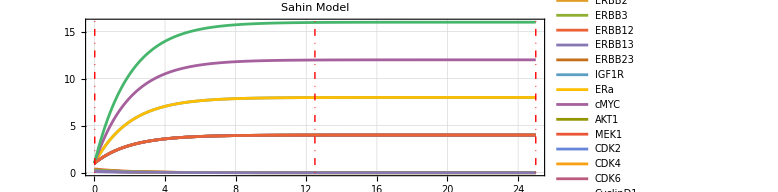

```mathematica
Plot[Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,25}]],{t,0,25}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel-> name, ImageSize->Large,Epilog-> {Thick,DotDashed, Red, Line[{{Epil[[1]],0},{Epil[[1]],20}}] ,Line[{{Epil[[2]],0},{Epil[[2]],20}}], Line[{{Epil[[3]],0},{Epil[[3]],20}}]}]
```

```mathematica
result=ThreeExperimentsBinarisation[IG,Values[exp], stablestate]
```

{<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→False,ERa→True,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→True,MEK1→True,p21→None,p27→None,pRB→True|>,<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→False,ERa→True,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→True,MEK1→True,p21→False,p27→False,pRB→True|>,<|AKT1→True,CDK2→True,CDK4→True,CDK6→True,cMYC→True,CyclinD1→True,CyclinE1→True,EGF→False,ERa→True,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→True,MEK1→True,p21→False,p27→False,pRB→True|>}

```mathematica
dis=Distanceofdissimilarity[result,stablestate] (*voir la fonction dans le package functionsneeded*)
```

{1/10,0,0}

### For stable state

```mathematica
stablestate=StableFB[[3]]
```

<|AKT1→False,CDK2→False,CDK4→False,CDK6→False,cMYC→False,CyclinD1→False,CyclinE1→False,EGF→False,ERa→False,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→False,MEK1→False,p21→False,p27→False,pRB→False|>

```mathematica
initialcondition=<|AKT1->0.3,CDK2->0.2,CDK4->0.4,CDK6->0.3,cMYC->0.1,CyclinD1->0.4,CyclinE1->0.2,EGF->0.3,ERa->0.3,ERBB1->0.3,ERBB12->0.3,ERBB13->0.3,ERBB2->0.3,ERBB23->0.3,ERBB3->0.3,IGF1R->0.3,MEK1->0.3,p21->0.3,p27->0.3,pRB->0.3|>
```

<|AKT1→0.3,CDK2→0.2,CDK4→0.4,CDK6→0.3,cMYC→0.1,CyclinD1→0.4,CyclinE1→0.2,EGF→0.3,ERa→0.3,ERBB1→0.3,ERBB12→0.3,ERBB13→0.3,ERBB2→0.3,ERBB23→0.3,ERBB3→0.3,IGF1R→0.3,MEK1→0.3,p21→0.3,p27→0.3,pRB→0.3|>

#### ODE

```mathematica
Framed@TableForm[
system=BooleanToODE[FB,t,κ,γ,θ, initialcondition,{hillm,hillp}]]
```

ERBB1'[t]==-0.5 ERBB1[t]+2 hillp[EGF[t],0.359521]
ERBB1[0]==0.3
ERBB2'[t]==-0.5 ERBB2[t]+2 hillp[EGF[t],0.359521]
ERBB2[0]==0.3
ERBB3'[t]==-0.5 ERBB3[t]+2 hillp[EGF[t],0.359521]
ERBB3[0]==0.3
ERBB12'[t]==-0.5 ERBB12[t]+2 hillp[ERBB1[t],0.648004] hillp[ERBB2[t],0.509802]
ERBB12[0]==0.3
ERBB13'[t]==-0.5 ERBB13[t]+2 hillp[ERBB1[t],0.648004] hillp[ERBB3[t],0.59708]
ERBB13[0]==0.3
ERBB23'[t]==-0.5 ERBB23[t]+2 hillp[ERBB2[t],0.509802] hillp[ERBB3[t],0.59708]
ERBB23[0]==0.3
IGF1R'[t]==2 (hillm[ERBB23[t],0.351322] hillp[AKT1[t],0.424898]+hillm[ERBB23[t],0.351322] hillp[ERa[t],0.458974])-0.5 IGF1R[t]
IGF1R[0]==0.3
ERa'[t]==-0.5 ERa[t]+2 (hillp[AKT1[t],0.424898]+hillp[MEK1[t],0.391763])
ERa[0]==0.3
cMYC'[t]==-0.5 cMYC[t]+2 (hillp[AKT1[t],0.424898]+hillp[ERa[t],0.458974]+hillp[MEK1[t],0.391763])
cMYC[0]==0.1
AKT1'[t]==-0.5 AKT1[t]+2 (hillp[ERBB1[t],0.648004]+hillp[ERBB12[t],0.600305]+hillp[ERBB13[t],0.649504]+hillp[ERBB23[t],0.351322]+hillp[IGF1R[t],0.503818])
AKT1[0]==0.3
MEK1'[t]==2 (hillp[ERBB1[t],0.648004]+hillp[ERBB12[t],0.600305]+hillp[ERBB13[t],0.649504]+hillp[ERBB23[t],0.351322]+hillp[IGF1R[t],0.503818])-0.5 MEK1[t]
MEK1[0]==0.3
CDK2'[t]==-0.5 CDK2[t]+2 hillm[p21[t],0.631795] hillm[p27[t],0.403053] hillp[CyclinE1[t],0.390616]
CDK2[0]==0.2
CDK4'[t]==-0.5 CDK4[t]+2 hillm[p21[t],0.631795] hillm[p27[t],0.403053] hillp[CyclinD1[t],0.568931]
CDK4[0]==0.4
CDK6'[t]==-0.5 CDK6[t]+2 hillp[CyclinD1[t],0.568931]
CDK6[0]==0.3
CyclinD1'[t]==-0.5 CyclinD1[t]+2 (hillp[AKT1[t],0.424898]+hillp[cMYC[t],0.507466]+hillp[ERa[t],0.458974]+hillp[MEK1[t],0.391763])
CyclinD1[0]==0.4
CyclinE1'[t]==-0.5 CyclinE1[t]+2 hillp[cMYC[t],0.507466]
CyclinE1[0]==0.2
p21'[t]==2 hillm[AKT1[t],0.424898] hillm[CDK4[t],0.37029] hillm[cMYC[t],0.507466] hillp[ERa[t],0.458974]-0.5 p21[t]
p21[0]==0.3
p27'[t]==2 hillm[AKT1[t],0.424898] hillm[CDK2[t],0.391851] hillm[CDK4[t],0.37029] hillm[cMYC[t],0.507466] hillp[ERa[t],0.458974]-0.5 p27[t]
p27[0]==0.3
pRB'[t]==2 hillp[CDK4[t],0.37029] hillp[CDK6[t],0.457385]-0.5 pRB[t]
pRB[0]==0.3
EGF'[t]==-0.5 EGF[t]+2 hillp[EGF[t],0.359521]
EGF[0]==0.3

#### Experiments

```mathematica
exp=ThreeExperienceFromODE[FB,system,25,stablestate,θ]
```

<|0.17→<|ERBB1→0.276,ERBB2→0.276,ERBB3→0.276,ERBB12→0.276,ERBB13→0.276,ERBB23→0.276,IGF1R→0.276,ERa→0.276,cMYC→0.0919,AKT1→0.276,MEK1→0.276,CDK2→0.184,CDK4→0.367,CDK6→0.276,CyclinD1→0.367,CyclinE1→0.184,p21→0.276,p27→0.276,pRB→0.276,EGF→0.276|>,12.57→<|ERBB1→0.000559,ERBB2→0.000559,ERBB3→0.000559,ERBB12→0.000559,ERBB13→0.000559,ERBB23→0.000559,IGF1R→0.000559,ERa→0.000559,cMYC→0.000186,AKT1→0.000559,MEK1→0.000559,CDK2→0.000373,CDK4→0.000746,CDK6→0.000559,CyclinD1→0.000746,CyclinE1→0.000373,p21→0.000559,p27→0.000559,pRB→0.000559,EGF→0.000559|>,25.→<|ERBB1→0,ERBB2→0,ERBB3→0,ERBB12→0,ERBB13→0,ERBB23→0,IGF1R→0,ERa→0,cMYC→0,AKT1→0,MEK1→0,CDK2→0,CDK4→0,CDK6→0,CyclinD1→0,CyclinE1→0,p21→0,p27→0,pRB→0,EGF→0|>|>

```mathematica
Epil=Keys[exp];
```

```mathematica
fun=#[t]&/@Keys[FB];
```

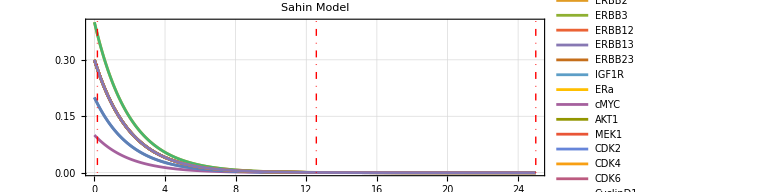

```mathematica
Plot[Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,25}]],{t,0,25}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel-> name, ImageSize->Large,Epilog-> {Thick,DotDashed, Red, Line[{{Epil[[1]],0},{Epil[[1]],20}}] ,Line[{{Epil[[2]],0},{Epil[[2]],20}}], Line[{{Epil[[3]],0},{Epil[[3]],20}}]}]
```

```mathematica
result=ThreeExperimentsBinarisation[IG,Values[exp], stablestate]
```

{<|AKT1→False,CDK2→None,CDK4→None,CDK6→False,cMYC→False,CyclinD1→False,CyclinE1→False,EGF→False,ERa→False,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→False,MEK1→False,p21→None,p27→None,pRB→None|>,<|AKT1→False,CDK2→False,CDK4→False,CDK6→False,cMYC→False,CyclinD1→False,CyclinE1→False,EGF→False,ERa→False,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→False,MEK1→False,p21→False,p27→False,pRB→False|>,<|AKT1→False,CDK2→False,CDK4→False,CDK6→False,cMYC→False,CyclinD1→False,CyclinE1→False,EGF→False,ERa→False,ERBB1→False,ERBB12→False,ERBB13→False,ERBB2→False,ERBB23→False,ERBB3→False,IGF1R→False,MEK1→False,p21→False,p27→False,pRB→False|>}

```mathematica
dis=Distanceofdissimilarity[result,stablestate]
```

{1/4,0,0}